# Leads connected to 1 - 10 and 41 to 50

# a1 and a3

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_]:= t*IdentityMatrix[10]
```

```mathematica
T[t_,m_]:=T[t,m]=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=t*IdentityMatrix[m];MAT]
```

```mathematica
Clear[leads]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[-3,3,0.01]}]
```

```mathematica
leads[10]
```

{1}
 |  |  |  |

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+301]]](*Module[{J=Inverse[β[ω,0.0001,1,0,m]],A:=Inverse[β[ω,0.0001,1,0,m]],T:=T1[1]},Do[J=Inverse[IdentityMatrix[m]-A.T.J.T].A,50000];J=J]*)
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[concentration_]:=dist[concentration]=Table[SortBy[Join[RandomSample[Join[s[1,25,1,12],s[26,50,13,50]],concentration],RandomSample[Join[s[1,25,13,50],s[26,50,1,12]],50-concentration]],First],1000]
```

```mathematica
ListPlot[{Join[s[1,25,1,12],s[26,50,13,50]],Join[s[1,25,13,50],s[26,50,1,12]],dist[5][[30]]},PlotMarkers->Automatic,PlotStyle->{Green,Green,Black},Axes->False]
```

```mathematica
TLD[t_]:=Module[{sizeoflead=10},Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{a,a},{a,41,50}]->t]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,50]]
```

```mathematica
SLLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
SRLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[41;;50,41;;50]]=LEFT[ω,m];MAT]
```

```mathematica
device1[ω_]:=Module[{sizeoflead=10},Inverse[IdentityMatrix[50]-g[ω,0.0001,1,0].T[1,sizeoflead].SLLEAD[ω,sizeoflead].T[1,sizeoflead]].g[ω,0.0001,1,0]]
```

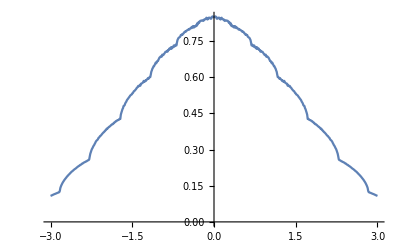

```mathematica
ListLinePlot[Table[{ω,-Im[LEFT[ω,10][[10,10]]]},{ω,Range[-3,3,0.01]}]]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,concentration_,number_]:= Module[{sizeoflead=10},
recurs=Module[{J1= device1[ω]},
Do[
J1=Inverse[IdentityMatrix[50]-Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[dist[concentration][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[concentration][[number]][[loc1,2]],dist[concentration][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,50}];J]].T[1,50].J1.T[1,50]].Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[dist[concentration][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[concentration][[number]][[loc1,2]],dist[concentration][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,50}];J]],{unitcell,50}];J1=J1];ir=Inverse[IdentityMatrix[50]-SRLEAD[ω,sizeoflead].TLD[1].recurs.TLD[1]].SRLEAD[ω,sizeoflead];il=Inverse[IdentityMatrix[50]-recurs.TLD[1].SRLEAD[ω,sizeoflead].TLD[1]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1].recurs;
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1].grr1.TLD[1]-TLD[1].GNON1.TLD[1].GNON1]];TRA]
```

```mathematica
LaunchKernels[4]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

```mathematica
Table[Export["/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2_right/50_ϵ1_conc_diag_"<>ToString[conc]<>"_.dat",Print[conc];Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,1,conc,n],{n,500}]]},{ω,Range[0,3,0.01]}]],{conc,5,45,5}]
```

{/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2_right/50_ϵ1_conc_diag_5_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2_right/50_ϵ1_conc_diag_10_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2_right/50_ϵ1_conc_diag_15_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2_right/50_ϵ1_conc_diag_20_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2_right/50_ϵ1_conc_diag_25_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2_right/50_ϵ1_conc_diag_30_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2_right/50_ϵ1_conc_diag_35_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2_right/50_ϵ1_conc_diag_40_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2_right/50_ϵ1_conc_diag_45_.dat}

```mathematica
transmission=Table[{x,Import["/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_3_4th_device_reading_2_right/50_ϵ1_conc_diag_"<>ToString[x]<>"_.dat"]},{x,Range[5,45,5]}]
```

{{5,{{0.,4.91132},{0.01,4.62299},{0.02,4.0208},{0.03,3.77156},{0.04,3.47578},{0.05,3.27265},{0.06,2.79472},{0.07,2.60498},{0.08,4.45084},{0.09,2.82659},{0.1,3.00403},{0.11,3.29228},{0.12,3.54146},{0.13,3.85932},{0.14,3.94556},272,{2.87,1.08401},{2.88,1.14927},{2.89,1.07889},{2.9,0.97715},{2.91,1.07431},{2.92,1.16858},{2.93,1.20403},{2.94,1.07883},{2.95,1.04552},{2.96,1.17729},{2.97,1.24255},{2.98,1.31998},{2.99,1.31932},{3.,1.24542}}},7,{45,{1}}}
 |  |  |  |

```mathematica
Dimensions[transmission]
```

{9,2}

```mathematica
input =Table[Print[n];ParallelTable[{ω,CA[ω,0.0001,1,0,1,25,n]},{ω,Range[0,3,0.01]}],{n,100}]
```

{{{0.,2.51768},{0.01,5.30385},{0.02,1.39723},{0.03,2.76198},{0.04,2.25173},{0.05,0.519348},{0.06,3.54791},{0.07,3.68611},{0.08,0.0646051},{0.09,2.30395},{0.1,4.78997},{0.11,3.34296},{0.12,1.69875},{0.13,4.75326},{0.14,1.45125},272,{2.87,0.442369},{2.88,1.13849},{2.89,1.14357},{2.9,0.427911},{2.91,0.0273749},{2.92,1.44164},{2.93,0.141075},{2.94,1.33815},{2.95,1.2705},{2.96,1.16152},{2.97,1.65298},{2.98,1.00656},{2.99,1.22612},{3.,0.528535}},98,{1}}
 |  |  |  |

```mathematica
misfit[x_,y_,n_]:=Module[{m5=input[[n]]},
ρ1=Table[{transmission[[con,1]],Module[{B1=Transpose[{m5[[1;;301]][[;;,1]],(m5[[1;;301,2]]-transmission[[con,2]][[1;;301,;;]][[;;,2]])^2}]},NIntegrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)(*+NIntegrate[Interpolation[B1][ω],{ω,-3,-0.5}]/((2.5)*100)*)]},{con,9}];lista=ρ1(*,ρ2,ρ3,ρ4*)(*,ρ5,ρ6*);
{lista,lista[[Position[lista,Min[lista]][[1,1]]]]}]
```

```mathematica
Table[misfit[1.5,0.2,n][[2]][[1]],{n,100}]
```

{10,15,20,45,25,15,25,25,25,20,30,25,20,10,40,25,25,15,35,30,15,10,25,15,20,5,25,25,25,15,15,15,25,35,35,40,25,25,20,25,35,25,20,15,25,40,5,20,20,25,40,20,35,30,30,35,30,30,45,15,15,25,40,30,15,15,20,15,20,30,20,20,5,25,15,20,20,30,20,20,25,30,15,25,25,15,15,20,15,20,25,10,20,30,15,30,20,20,30,10}

```mathematica
gg[y_]:=Table[Table[misfit[x+y,x,n][[2]][[1]],{x,Range[0,1.5,0.1]}],{n,100}]
```

```mathematica
Table[gg[y],{}]
```

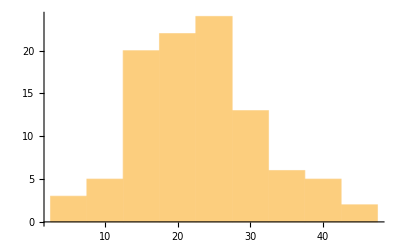

```mathematica
Histogram[%27]
```

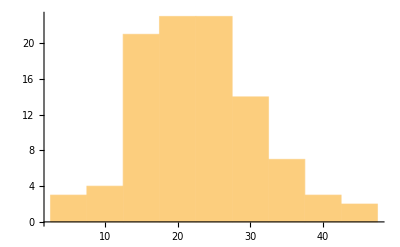

```mathematica
Histogram[%25]
```

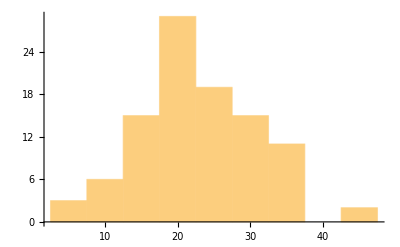

```mathematica
Histogram[%23]
```

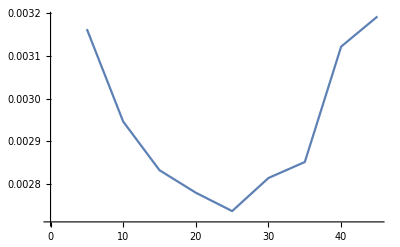

```mathematica
ListLinePlot[misfit[03,00.5,9][[1]]]
```

```mathematica
[misfit[03,0.5,9][[2]]]
```

{25,0.00273614}

```mathematica
{{5,0.0031631572334185256},{10,0.0029461647302388093},{15,0.0028319920137103187},{20,0.0027791875299745736},{25,0.0027361389424542743},{35,0.002851252769790251},{45,0.003192806641765258}}
```

{{5,0.00316316},{10,0.00294616},{15,0.00283199},{20,0.00277919},{25,0.00273614},{35,0.00285125},{45,0.00319281}}

```mathematica
Interpolation[%83]
```

InterpolatingFunction[…]

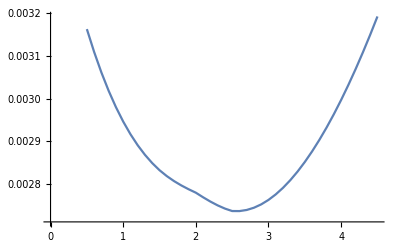

```mathematica
ListLinePlot[Table[{x/10,%84[x]},{x,Range[5,45,01]}]]
```

```mathematica
Table[{(x)/10,%84[x]},{x,Range[5,45,01]}]
```

{{1/2,0.00316316},{3/5,0.00310954},{7/10,0.00306137},{4/5,0.0030183},{9/10,0.00298001},{1,0.00294616},{11/10,0.00291643},{6/5,0.00289048},{13/10,0.00286798},{7/5,0.00284859},{3/2,0.00283199},{8/5,0.00281817},{17/10,0.0028064},{9/5,0.00279625},{19/10,0.00278732},{2,0.00277919},{21/10,0.00276842},{11/5,0.00275839},{23/10,0.00274944},{12/5,0.0027419},{5/2,0.00273614},{13/5,0.00273603},{27/10,0.00273864},{14/5,0.00274391},{29/10,0.0027518},{3,0.00276225},{31/10,0.00277522},{16/5,0.00279066},{33/10,0.00280851},{17/5,0.00282872},{7/2,0.00285125},{18/5,0.00287605},{37/10,0.00290306},{19/5,0.00293223},{39/10,0.00296351},{4,0.00299686},{41/10,0.00303223},{21/5,0.00306955},{43/10,0.00310879},{22/5,0.00314989},{9/2,0.00319281}}

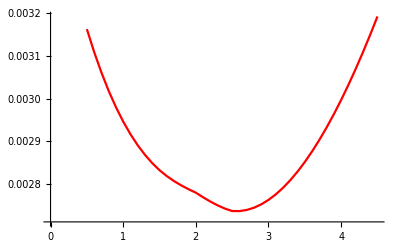

```mathematica
ListPlot[%89,Joined->True,PlotStyle->Red]
```

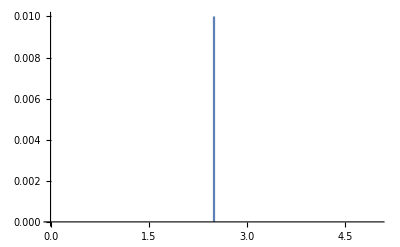

```mathematica
ListLinePlot[Table[{2.5,y},{y,Range[0,0.01,0.00001]}]]
```

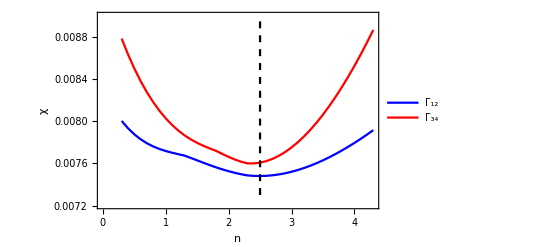

```mathematica
ListPlot[{%60,Table[{(x-2)/10,%84[x]/0.36},{x,Range[5,45,01]}],Table[{2.5,y},{y,Range[0.0073,0.00900,0.00001]}]},Joined->True,PlotStyle->{Blue,Red,{Black,Dashed}},Frame->True,PlotLegends->Placed[LineLegend[{"Γ_12","Γ_34"},(*LegendLabel->"label",*)LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],Above],FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]}]
```

```mathematica
Export["/home/shardulmukim/PhD/quantum_sudoq/misfit_fig_1.pdf",%167]
```

/home/shardulmukim/PhD/quantum_sudoq/misfit_fig_1.pdf

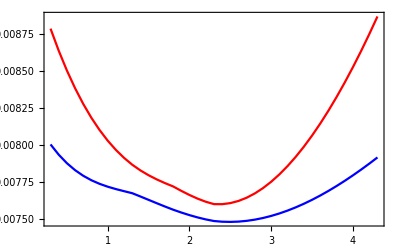

```mathematica
Show[ListPlot[,Joined->True,Frame->True,PlotStyle->Blue],ListPlot[{%60,Table[{(x-2)/10,%84[x]/0.36},{x,Range[5,45,01]}],Table[{2.5,y},{y,Range[0.0073,0.00900,0.00001]}]},Joined->True,PlotStyle->Red](*,PlotStyle->Black],PlotRange->All*),PlotRange->All]
```

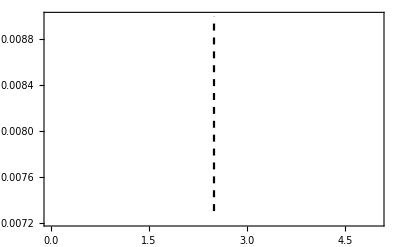

```mathematica
ListLinePlot[Table[{2.5,y},{y,Range[0.0073,0.00900,0.00001]}],PlotStyle->{Black,Dashed},Frame->True]
```

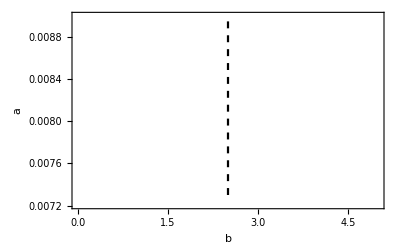

```mathematica
Show[%159,FrameLabel->{{HoldForm[a],None},{HoldForm[b],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]}]
```

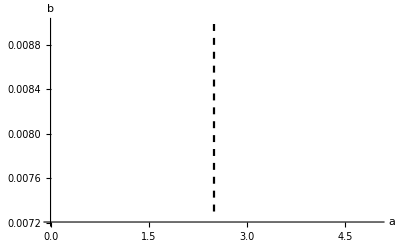

```mathematica
Show[%119,AxesLabel->{HoldForm[a],HoldForm[b]},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]}]
```

```mathematica
Show[%118,%119,PlotLegends]
```

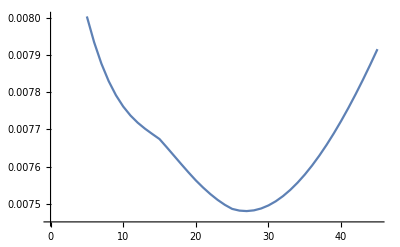

```mathematica
ListPlot[%51,Joined->True]
```

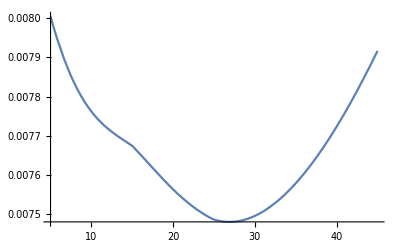

```mathematica
Plot[%49[x],{x,5.,45.},Plo]
```

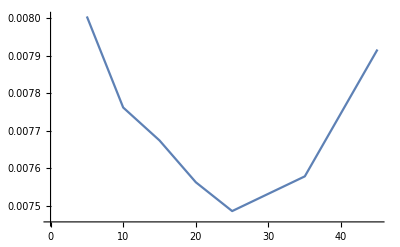

```mathematica
ListPlot[In[{{5,0.008004060461523813},{10,0.0077617753527776424},{15,0.007674170763726392},{20,0.0075628754130396564},{25,0.007486225252870183},{35,0.007578618407504398},{45,0.007916078212254688}}],Joined->True]
```

```mathematica
N[57/2]
```

28.5

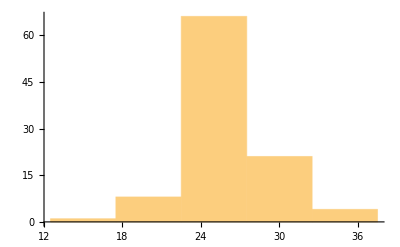

```mathematica
Histogram[%55]
```